# HRT Problem

## Strong stability in the Hospitals/Residents with Ties Problem

## Задача Госпиталей/Резидентов (Hospitals/Residents)

Hospitals/Residents Problem (HR) - это одно из расширений проблемы стандартного марьяжа. 
Постановка задачи включает в себя два набора: набор R резидентов и набор H госпиталей. 
Каждый резидент r ∈ R должен быть назначенным только в одну больницу, а каждая больница h ∈ H имеет квоту q.

Каждый госпиталь ранжирует некоторых резидентов в строгом порядке своего предпочтения
Каждый резидент ранжирует некоторые госпитали в строгом порядке своего предпочтения
-Graphics--Graphics-
Согласованность списков предпочтений (consistence) заключается в том, что резидент 
присутствует в списке предпочтений какого-то госпиталя тогда и только тогда, 
когда сам госпиталь присутствет в списке предпочтений данного резидента. Она подразумевается везде далее

## Задача Госпиталей/Резидентов (Hospitals/Residents)

Распределение (matching) - множество пар госпиталей и резидентов, в котором каждый резидент должен быть назначенным не более  в одну больницу, а каждая больница получила число резидентов, не превышающее её квоту q.

Распределение считается стабильным (stable), если не существует такой пары (r,h), которые не назначены друг другу в распределении, но при этом резиденту выгодно сменить госпиталь, а госпиталю - заменить какого-нибудь из текущих резидентов этим. 

Такая пара называется блокирующей (blocking pair). Например, ниже такой парой являются резидент 2 и госпиталь 1. 
Последний не против взять резидента 2 вместо третьего, а для резидента 2, в свою очередь, госпиталь 1 более предпочтителен, чем госпиталь 2, в который он на данный момент распределён:
-Graphics-
Задача HR заключается в том, чтобы найти стабильное распределение! 
Решение данной задачи известно и осуществляется модификацией алгоритма Gale/Shapley

## Задача Госпиталей/Резидентов с ничьями (Hospitals/Residents with Ties)

Hospitals/Residents Problem with Ties (HR) - это одно из расширений HR. 

Теперь порядок в списках предпочтениях может быть нестрогий (везде ниже знак ≥ подразумевает, что достигается равенство с точки зрения предпочтений): 
-Graphics--Graphics-

## Определения стабильностей

В связи с модифициранной постановкой задачи возникает несколько видов стабильностей!
Блокирующей парой является пара (r,h) которые не назначены друг другу, где:

1) Cлабая стабильность (weak stable)

Резиденту r - строго выгодно сменить госпиталь на h
Госпиталю h - строго выгодно заменить какого-нибудь из текущих резидентов на r

2) Сильная стабильность (strong stable)

Резиденту r - нестрого выгодно сменить госпиталь на h
Госпиталю h - строго выгодно заменить какого-нибудь из текущих резидентов на r
ИЛИ
Резиденту r - строго выгодно сменить госпиталь на h
Госпиталю h - нестрого выгодно заменить какого-нибудь из текущих резидентов на r

3) Суперстабильность (super stable)

Резиденту r - нестрого выгодно сменить госпиталь на h
Госпиталю h - нестрого выгодно заменить какого-нибудь из текущих резидентов на r

Авторы статьи считают наиболее разумным требованием к распределению strong stability. 
Временная сложность реализованного ниже алгоритма из статьи O(a^2) где a - это количество предпочтений

## Генерирование случайных данных

В коде реализована генерация случайных данных для постановки задачи

Ничьи (ties) реализованы с помощью группировки по подспискам - все резиденты/госпитали из одного подсписка считаются равноценными в данном списке предпочтений

```mathematica
MatrixForm[GeneratedRprefs]
MatrixForm[GeneratedHprefs]
MatrixForm[GeneratedQuotas]
```

({{1}}
{{5}}
{{2},{1},{5}}
{{1},{3},{2,5}}
{{2},{5}}
{{5,3},{4}}
{{2}}
{{4},{5},{2}}
{{1}}
{{1},{5},{3}}
{{4}}
{{1},{2}}
{{1}}
{{1,3},{4},{5}}
{{3}}
{{5},{2,1}}
{{2},{5},{4}}
{{2},{1},{4}}
{{3}}
{{4,5,3},{1}})

({{9},{1},{20,12},{13},{4,3},{16},{18},{14},{10}}
{{12},{5,16},{4},{17},{8},{3,7},{18}}
{{20},{10},{15},{6,4},{14},{19}}
{{20},{14},{18},{11},{8},{17},{6}}
{{2,20},{4},{6,5},{17},{3},{8},{10},{16},{14}})

(1
4
3
1
5)

## Вспомогательная функция Find Alternating Path

Альтернирующий путь относительно подмножества ребёр M (alternating path) - такой путь в графе, рёбра которого поочерёдно то не принадлежат, то принадлежат M

Пример работы функции:

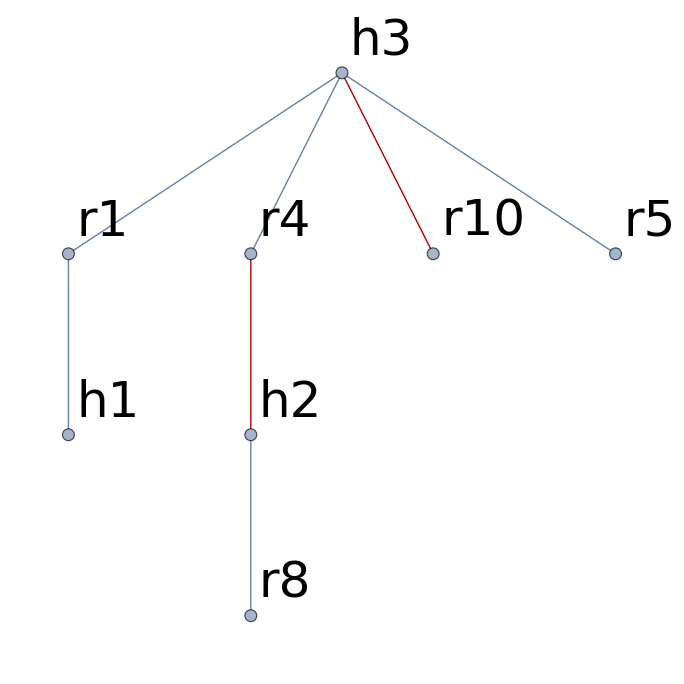

Найден альтернирующий путь:{r8<->h2,r4<->h2,r4<->h3}

```mathematica
ExampleGraph = Graph[
{"r1"<->"h1","r4"<->"h2","r8"<->"h2","r1"<->"h3","r4"<->"h3","r10"<->"h3","r5"<->"h3"}, VertexLabels->"Name",VertexLabelStyle->Directive[Black,Italic,50]];
ExampleM = {"r4"<->"h2","r10"<->"h3"};
ap = FindAlternatingPath[ExampleGraph, "r8","h3",ExampleM];
hg = HighlightGraph[ExampleGraph, ExampleM];
Print[hg];
Print["Найден альтернирующий путь:",ap]
```

## Функция Find Maximum Matching

С использованием Find Alternating Path реализует итеративный алгоритм поиска распределения M с максимальным числом ребёр в графе с квотами.

Идея:
1) Начать с M={}
2) Искать альтернирующие пути от свободных резидентов в пока незаполненые госпитали
3) Если существует такой альтернирующий путь p , то M⊕p увеличивает размер M на 1 при сохранении всех ограничений
4) Финальное множество M выдаётся как результат работы функции:

Кроме того, функция находит критическое множество Z (см. далее)

Найдём распределение в графе:

Critical set Z ={}

{r1<->h1,r10<->h3,r4<->h3,r5<->h3,r8<->h2}

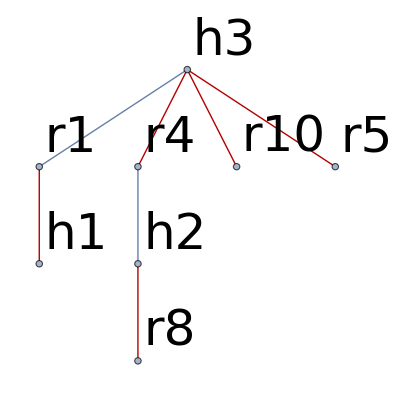

```mathematica
listExampleGraph = {{1},{4,8},{1,4,5,10},{},{}};
FoundMatching = FindMaximumMatching[listExampleGraph, ExampleGraph, {1, 1, 3}]
HighlightGraph[ExampleGraph, FoundMatching]
```

## Функция Find Maximum Matching

Пример итеративного шага

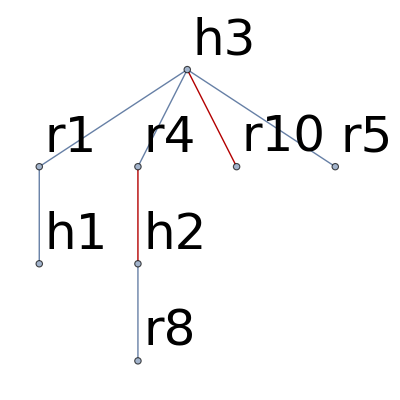

{r8<->h2,r4<->h2,r4<->h3}

```mathematica
hg
ap
```

r8 не попал ни в какой в госпиталь. Однако, если в h3 ещё есть места, то r8 может договориться с r4, что тот пойдёт не в h2, а в h3, тем самым освобождая r8 место в h2. 

Математически такое преобразование получается через XOR текущего множества M с найденным альтернирующим путём: M⊕ap

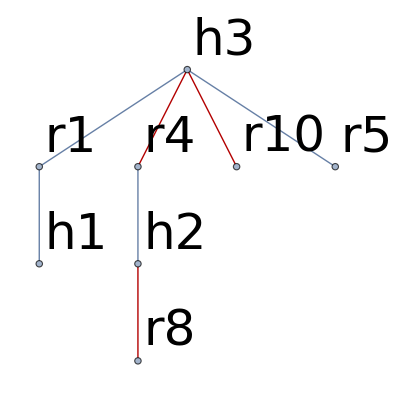

```mathematica
ExampleM = Complement[Union[ExampleM,ap],Intersection[ExampleM,ap]]; (*XOR of matching ExampleM and path ap*)
HighlightGraph[ExampleGraph, ExampleM]
```

## АЛГОРИТМ

-Graphics-

## Предварительное назначение резидентов

Основной цикл алгоритма начинается с предварительного назначения резидентов в head их списка предпочтений - т.е. первый подсписок госпиталей, куда они хотят.
-Graphics-
Данная информация хранится в графе предварительных назначений G (provisional assignment graph), для удобства он имеет вид таблицы:

```mathematica
G
```

{{9},{5,12,16,4},{15,20,10},{20},{2,6,20,4,17}}

```mathematica
{{3,5},{4,6,7,9},{2,8,10}}
```

{{3,5},{4,6,7,9},{2,8,10}}

## Удаление доминируемых резидентов

В результате предварительных назначений некоторые госпитали могут оказаться заполнеными или переполненными. Из таких госпителей следует удалить пары резидентов, которые доминируются нём

Резидент r доминируется в госпитале h (is dominated in h), если существует не менее чем ph (квота данного госпиталя) резидентов, 
уже предварительно назначенных в госпиталь и строго лучше r. 
   
Удаление пары (r,h) - это удаление r и h из списков предпочтений друг друга (HPrefs и Rprefs) и отмена предвательного назначения  в G, если таковое имелось. 

-Graphics-
После удаления доминируемых резидентов процесс предварительного назначений со слайда выше возобновляется,  пока есть свободные резиденты с непустым списком предпочтений
-Graphics-

## Reduced assignment graph

Как только все резиденты назначены (либо их список стал пустым в результате удаления и они больше ни на что не претендуют), запускается процесс нахождения редуцированного графа предварительных назначений GR (reduced provisional assignment graph)

Он формируется из G следующим образом:

1) Ищем привязанных (bound) резидентов в каждом госпитале
Резидент считается привязанным в госпитале h, если либо госпиталь не заполнен/переполнен, либо резидент не в хвосте(tail) - последнем подсписке списка предпочтений данного госпиталя.
2) Удаляем ребро привязанного к госпиталя резидента, а также все иные исходящие из резидента рёбра. 
3) Уменьшаем квоту госпиталя на 1 после удаления ребра. Получившиеся значения - пересмотренные квоты (revised quota)
4) Если пересмотренная квота какого-то госпиталя снизилась до 0, то удаляем госпиталь из графа.

```mathematica
G
Quotas

GR
RevisedQuotas
```

{{9},{5,12,16,4},{15,20,10},{20},{2,6,20,4,17}}

{1,4,3,1,5}

{{},{},{},{},{}}

{0,0,0,1,2}

## Критическое множество

Критическое множество Z (critical set) - это множество резидентов в GR с максимальным дефицитом мест в госпиталях, куда они предварительно назначены.

По лемме 6 статьи,  Z = U + U', где
 U - unassigned residents (неназначенные в соответсвии M)
 U' - резиденты достижимые из резидентов U через альтернирующий путь.

Функция Find Maximum Matching одновременно с итеративным нахождением максимальное соответствия M считает критическое множество Z.

Окрестность N(Z) (neighbourhood of Z) - множество госпиталей, куда предварительно назначены резиденты критического множества.

В соответствии со стаьёй, пары из хвоста N(Z) должны быть удалены.

После этого основной цикл программы запускается заново, и так  до пока какая-то из итераций не выдаст пустое критическое множество
-Graphics-

## Финальный ответ

Находим возможное распределение в финальном графе предварительных назначений:

```mathematica
GEdges = Flatten[Table[Table[("r"<>ToString[ G[[i]][[j]] ])<->("h"<>ToString[i]),{j,Length[G[[i]]] } ],{i,Length[G]}],2];
Ggraph=Graph[GEdges, VertexLabels->"Name",VertexLabelStyle->Directive[Black,Italic,40]];
Matching =FindMaximumMatching[G, Ggraph,Quotas]
```

Critical set Z ={}

{r10<->h3,r11<->h4,r12<->h4,r16<->h4,r17<->h2,r19<->h3,r2<->h5,r20<->h2,r3<->h4,r5<->h1,r6<->h2,r7<->h3,r8<->h1,r9<->h2}

```mathematica
{"r10"<->"h3","r2"<->"h3","r3"<->"h1","r4"<->"h2","r5"<->"h1","r6"<->"h2","r7"<->"h2","r8"<->"h3","r9"<->"h2"}
```

{r10<->h3,r2<->h3,r3<->h1,r4<->h2,r5<->h1,r6<->h2,r7<->h2,r8<->h3,r9<->h2}

Есть определённые условия, при которых найденное возможное распределение действительно будет удовлетворять условиям сильной стабильности. 
А именно число резидентов в M:
1) для незаполненных госпиталей - должно быть не меньше чем число предварительно назначенных резидентов в G
2) для заполненных и переполненных - должно быть не меньше квоты

Вычислим Req - необходимое число резидентов в распределении для любого госпиталя:

```mathematica
HospitalVertices= Select[VertexList[Ggraph],StringTake[#,1]=="h"&];
HospitalDegrees = Table[VertexDegree[Ggraph,HospitalVertices[[i]]],{i,Length[HospitalVertices]}];
MatchingGraph = Graph[Matching , VertexLabels->"Name"];
MatchingHospitalDegrees = Table[VertexDegree[MatchingGraph,HospitalVertices[[i]]],{i,Length[HospitalVertices]}];

QuotasForGraphHospitals = Quotas[[ToExpression[StringDrop[HospitalVertices,1] ]]];
Req = MapThread[Min,{HospitalDegrees,QuotasForGraphHospitals}]
```

{2,4,3,4,2}

## Финальный ответ

Теперь достаточно проверить, удовлетворяет ли требованием найденный matching.
В случае положительного ответа он и будет являться искомым сильно стабильным распределением
В случае отрицательного ответа, по лемме, ни найденное, ни какое-нибудь другое не будет подходить, и на экран будет выведен результат, что сильно стабильное распределение не существует

No strongly stable matching exists

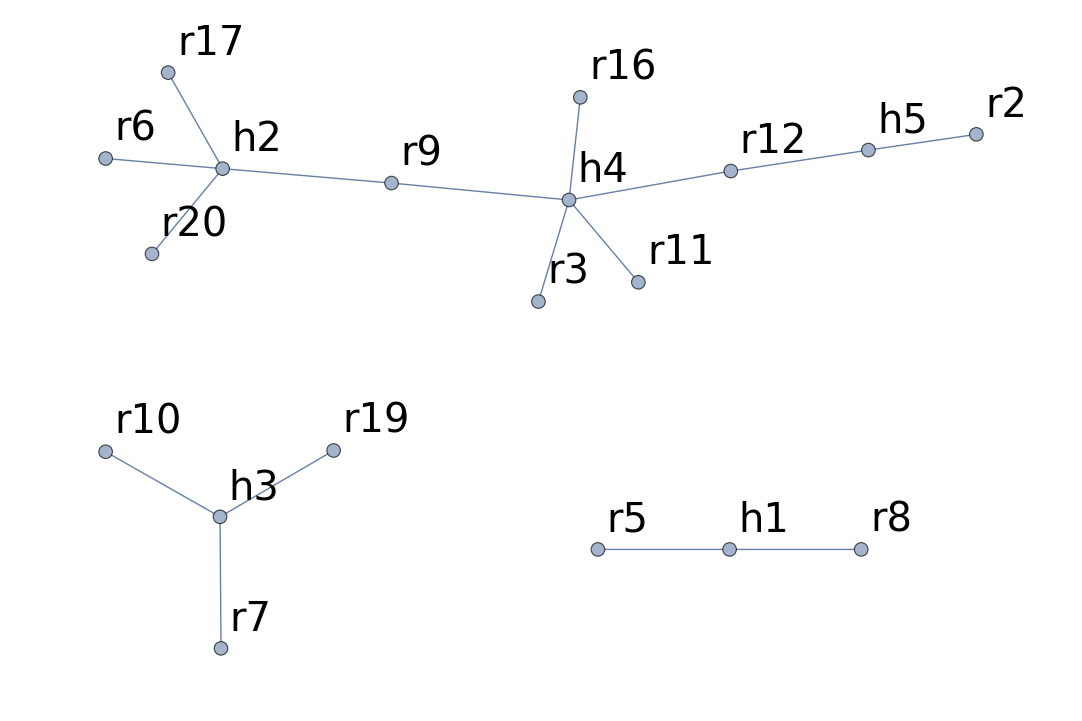

```mathematica
If [Max[Req - MatchingHospitalDegrees]>0,
Print["No strongly stable matching exists"];
Print[Ggraph];
,
Print["Strong stable matching:"];
Print[MatrixForm[Matching]];

Mgraph = HighlightGraph[Ggraph,Matching ];

Print[Mgraph];

];
```

## Код программы

```mathematica
HRT PROBLEM
```

RANDOM DATA GENERATION

```mathematica
(*Input of hospitals and residents quantities*)
R=20;
H=5;

(*Initialisation of preferenses with epmty list for each hospital/resident*)
GeneratedRprefs = Table[List[],{i,R}];
GeneratedHprefs=Table[List[],{i,H}];

(*Initialisation of quotas for each hospital*)
GeneratedQuotas=Table[1,{i,H}];

(*Manually set distribution parameters for dataset*)
QuotaLimit = 5;
RTDP= 10; (*ResidentsTiesDistributionParameter *)
HTDP= 20; (*HospitalsTiesDistributionParameter *)


(*Table of applications to hospitals by residents, required for generation a consistent dataset*)
AppliedResidentsTable = Table[List[],{i,H}];

(*RESIDENTS PREFERENCES GENERATION LOOP*)
For[thisResident=1, thisResident ≤R,thisResident ++,

	thisResidentPrefLength = RandomInteger[{1,H}];
	k = RandomSample[Range[H],thisResidentPrefLength]; (*Random sample without ties*)
	GeneratedRprefs[[thisResident]] = k;

	AppliedResidentsTable[[k]] = Map[Append[#,thisResident]&,AppliedResidentsTable[[k]] ];
	GeneratedRprefs[[thisResident]] =  GatherBy[GeneratedRprefs[[thisResident]],RandomInteger[RTDP]&];  (*Sample gathered in ties randomly*)
]

(*HOSPITALS PREFERENCES AND QUOTAS GENERATION LOOP*)
For[thisHospital=1, thisHospital ≤H,thisHospital++,
		
		GeneratedQuotas[[thisHospital]] =  RandomInteger[{1,QuotaLimit}]; (*Random quota value*)
		
		(*Random sample without ties from applicants to this Hospital. Thus we garantee preference list are consistent*)
		GeneratedHprefs[[thisHospital]] =RandomSample[AppliedResidentsTable[[thisHospital]] ] ;

		GeneratedHprefs[[thisHospital]] =  GatherBy[GeneratedHprefs[[thisHospital]],RandomInteger[HTDP]&];   (*Sample gathered in ties randomly*)
];
```

GENERATED DATA

```mathematica
(*remove semicolon to observe*)
MatrixForm[GeneratedRprefs]
MatrixForm[GeneratedHprefs]
MatrixForm[GeneratedQuotas]
```

({{5},{1},{2},{3}}
{{5}}
{{1},{4},{5},{2}}
{{1},{3},{5}}
{{1,2},{4},{5},{3}}
{{2},{3},{4,1,5}}
{{1,5,4},{3},{2}}
{{5},{1},{4}}
{{4,2},{5},{1}}
{{3}}
{{3,2},{4},{1},{5}}
{{2},{3},{5,4},{1}}
{{1},{5},{3}}
{{1},{5},{3}}
{{1}}
{{4},{2},{5},{3},{1}}
{{1},{2},{4,3},{5}}
{{5}}
{{3},{2},{5},{1}}
{{5},{2}})

({{8,5},{12,7},{13},{3,4,9},{16},{19,1},{17,6},{14,15},{11}}
{{20},{6},{3},{17},{9},{19},{7},{1,11},{12},{16},{5}}
{{10},{19,7},{17},{11},{12},{5},{1,4},{14},{16},{13},{6}}
{{11,6},{16},{5},{17},{12},{9,3},{7},{8}}
{{2,12},{17,5},{20,13},{11},{7,8},{9},{18},{14,19},{3},{6,16},{4,1}})

(2
4
3
4
2)

```mathematica
FUNCTIONS
```

```mathematica
(*Find an alternating path with respect to Matching from resident rN to hospital hN
Returns the first found alternating pathas a list of edges
 OR empty list {} if nothing found *)

FindAlternatingPath[GRAPH_, startVertice_,finalVertice_, Matching_]:=
Module[
{G=GRAPH,s= startVertice,f= finalVertice},

(*find all paths and represent it as a list of edges*)
paths=FindPath[G, s, f,2*H,All];
pathsAsEdgeLists = EdgeList/@(PathGraph/@paths);

path ={};

(*Loop over all found paths*)
For[k=1, k<=Length[paths],k++,

path =pathsAsEdgeLists[[k]];

OddEdgesInPath = path [[1;;;;2]]; (* 1st, 3rd, 5th ... edges*)
EvenEdgesInPath = path [[2;;;;2]];(* 2nd, 4th, 6th ... edges*)

EvenEdgesInPath =EdgeList[PathGraph[Reverse[VertexList[EvenEdgesInPath]]]] ;
path [[2;;;;2]]= EvenEdgesInPath;
(*a crutch that is necessary so that there is always a resident at the beginning of the edge and checking the set of edges for the fact that this is a matching subset was correct*)
(*Check if the path is alternating*)
If [SubsetQ[Matching, EvenEdgesInPath]&&Intersection[OddEdgesInPath ,Matching]=={},
(*Yes.  break cycle and return this path*)
Break[];
,
(*No. Discard the path*)
path ={};
];
];
Return[path,Module]
];
```

```mathematica
FindMaximumMatching[listG_,GRAPH_,RevisedQuotas_]:=
Module[
{lG = listG,G=GRAPH,RQ =RevisedQuotas},
M ={};
U = {}; (*Unassigned*)
Uprime={};(*U' - reachable from this unassigned residents via alternating paths*)


GRResidents =DeleteDuplicates[Flatten[lG]];
GRHospitals = Select[Range[H],(lG[[#]]!={})&];

For[i=1,i≤Length[GRResidents],i++,
r=GRResidents[[i]];
p = {};

For[j=1,j≤Length[GRHospitals],j++,
h =GRHospitals[[j]];

residentVertice = "r"<>ToString[r];
hospitalVertice = "h"<>ToString[h];

If[RQ[[h]]≥1,

p = FindAlternatingPath[G, residentVertice,hospitalVertice, M];

If[p≠{},
(*resident r has  alternating path to free hospital *)
M = Complement[Union[M,p],Intersection[M,p]]; (*XOR of matching M and path p*)
RQ[[h]] -=1;
Break[]
];
];

If[j==Length[GRHospitals]&&p == {},
(*resident r has no alternating paths to free hospitals *)
AppendTo[U,r];

(*Find U'  - reachable from this unassigned resident via alternating path*)
For[l=1,l≤Length[GRResidents ],l++,
rZcandidate=GRResidents [[l]];
rZcandidateVertice = "r"<>ToString[rZcandidate];

If[FindAlternatingPath[G, residentVertice,rZcandidateVertice, M]≠{},
AppendTo[Uprime,rZcandidate];
];
];
];
];
];

Z = Union[U,Uprime];

Print["Critical set Z =", Z];
Return[M,Module]
]
```

ALGORITHM

```mathematica
Rprefs= GeneratedRprefs;
Hprefs = GeneratedHprefs;
Quotas = GeneratedQuotas;


Z = Range[R];
(*G=  Table[List[],{i,H}]; Provisional assignment graph *)
GR= G;
z =1;

While[Z != {},
Print ["-------------------------------------------"];
Print ["ITERATION ", z];
G=  Table[List[],{i,H}]; (*Provisional assignment graph *)

 	For[j=1,j<20,j++,
		(* Provisional assignment iterantion j .Build provisional assignment graph *)
		For[r=1,r≤R,r++,
			If [Position[G,r]=={} && Rprefs[[r]]≠{},
				rh = Rprefs[[r]][[1]];

				G[[rh]] = Map[Append[#,r]&,G[[rh]] ];
			];
		];
		(*Print["G = ", G];*)

		(*Loop over hospitals to find replete ones *)
		For[h=1,h<=H,h++,
			If[Length[G[[h]]]≥Quotas[[h]], (* Hospital  h is replete*)

				(*Loop over residents from Hprefs to find dominated ones in current replete hospital h*)
				HprefsFlattened = Flatten[Hprefs[[h]]];
				
				For[i=1,i<=Length[HprefsFlattened],i++,
						r = HprefsFlattened[[i]];
						pos= Position[Hprefs[[h]],r];
						p = pos[[1]][[1]];
					
						ResidentsBetter =Flatten[Hprefs[[h]][[Range[p-1] ]] ]; (*all resident better*)
						ProvisionallyAssignedResidentsBetter = Intersection[ResidentsBetter, G[[h]] ] ;(*intersection with provisionally assigned*)
						l =Length[ ProvisionallyAssignedResidentsBetter];
						
						If[l≥Quotas[[h]],
							(*Print["resident №", r, " is dominated in hospital  №", h, ". Deletion..."];*)
							
							(*Delete them from one another's preference lists*)
							Hprefs[[h]] =Replace[ Delete[ Hprefs[[h]],pos], {}->Nothing,{1,2}]; (*replace with levelspec = {1,2} deletes empty ties*)
							
							
							Rprefs[[r]] = Replace[Delete[ Rprefs[[r]],Position[Rprefs[[r]],h]], {}->Nothing,{1,2}]; (*replace with levelspec = {1,2} deletes empty ties*)
							
							(*If r is provisionally assigned to h,the breaking of this provisional assignment *)
							If [Position[G[[h]],r]≠{},
								G[[h]] = Delete[G[[h]], Position[G[[h]],r] ];
							];
						];
					];
				];
			];
		];

		(*Build REDUCED provisional assignment graph *)
				GR = G;
				
				RevisedQuotas = Quotas;
				For[h=1,h<=H,h++,
					If[GR[[h]]≠{},
						ProvisionallyAssignedResidents = GR[[h]];
						For[k=1,k<=Length[ ProvisionallyAssignedResidents],k++,
							
							r = ProvisionallyAssignedResidents[[k]];

							pos= Position[Hprefs[[h]],r];
							p = pos[[1]][[1]];
						
							If[(Length[GR[[h]]]<=RevisedQuotas[[h]]) ||(p<Length[Hprefs[[h]]]),
								(*Removing *)
								GR = Delete[GR, Position[GR,r] ];
								RevisedQuotas[[h]] -= 1;
							];
							
							If[RevisedQuotas[[h]] == 0,
								GR[[h]]={};
								Break[];
							];
						];
					];
				];
			Print["Provisional assignment graph  G= ",G];
			Print["Reduced Graph  GR= ",GR];
		GREdges = Flatten[Table[Table[("r"<>ToString[ GR[[i]][[j]] ])<->("h"<>ToString[i]),{j,Length[GR[[i]]] } ],{i,Length[GR]}],2];
		GRgraph=Graph[GREdges, VertexLabels->"Name",VertexLabelStyle->Directive[Black,Italic,50]];

		(*Find matching and critical set Z*)
		M =FindMaximumMatching[GR,GRgraph,RevisedQuotas];

		Print["Matching in GR"];
		Print[HighlightGraph[GRgraph,M]];
  		ZVertex = Table["r"<>ToString[ Z[[i]] ],{i,Length[Z]}];

		(*Find N(Z) *)
		NG =NeighborhoodGraph[GRgraph,ZVertex ];
		NofZ =Select[VertexList[NG ],StringTake[#,1]=="h"&];

		(*Find N(Z) as a number list, not {"h22", "h145"} form *)
		NZlist =ToExpression[StringDrop[NofZ,1] ];

		(*DELETE TAILS *)

		For[hv=1,hv≤Length[NZlist],hv++,

			h =NZlist[[hv]];
			rdeletionlist = DeleteDuplicates[Flatten[Hprefs[[h,-1]] ,3]];

			(*If r is provisionally assigned to h,the breaking of this provisional assignment *)
			For[dr = 1, dr ≤Length[rdeletionlist], dr++,
				delr =rdeletionlist[[dr]];
				
				If [Position[G[[h]],delr ]≠{},
				G[[h]] = Delete[G[[h]], Position[G[[h]],delr] ];
					];
			];

		(*Delete them from one another's preference lists*)
		pos=Position[Rprefs[[  Hprefs[[h,-1]]  ]],h];
		Rprefs[[  Hprefs[[h,-1]] ]] =Replace[Delete[ Rprefs[[  Hprefs[[h,-1]] ]],pos],{}->Nothing, {2,3}]; (*replace with levelspec = {2,3} deletes empty ties*)  

		Hprefs[[h]] =Replace[ Delete[ Hprefs[[h]],-1], {}->Nothing,{2,3}]; (*replace with levelspec = {1,2} deletes empty ties*) 
			];
	z++;
];
```

-------------------------------------------

ITERATION 1

Provisional assignment graph  G= {{5,8},{6,9,17,20},{10,19,7},{9,16,3,12,11},{2,12}}

Reduced Graph  GR= {{},{},{},{},{}}

Critical set Z ={}

Matching in GR

-Graphics-

Critical set Z ={}

No strongly stable matching exists

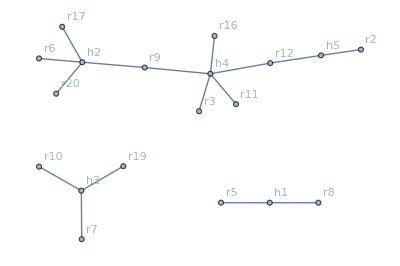

```mathematica
(*Feasible matching in provisional assignment graph*)
GEdges = Flatten[Table[Table[("r"<>ToString[ G[[i]][[j]] ])<->("h"<>ToString[i]),{j,Length[G[[i]]] } ],{i,Length[G]}],2];
Ggraph=Graph[GEdges, VertexLabels->"Name"];
Matching =FindMaximumMatching[G,Ggraph,Quotas];

(*Calculating Req - required number of residents in matching for hospitals - the vertex degree in G or its quota for each particular h *)
HospitalVertices= Select[VertexList[Ggraph],StringTake[#,1]=="h"&];
HospitalDegrees = Table[VertexDegree[Ggraph,HospitalVertices[[i]]],{i,Length[HospitalVertices]}];
MatchingGraph = Graph[Matching , VertexLabels->"Name"];
MatchingHospitalDegrees = Table[VertexDegree[MatchingGraph,HospitalVertices[[i]]],{i,Length[HospitalVertices]}];

QuotasForGraphHospitals = Quotas[[ToExpression[StringDrop[HospitalVertices,1] ]]];
Req = MapThread[Min,{HospitalDegrees,QuotasForGraphHospitals}] ; 


(*ANSWER*)
If [Max[Req - MatchingHospitalDegrees]>0,
Print["No strongly stable matching exists"];
Print[Ggraph];
,
Print["Strong stable matching:"];
Print[MatrixForm[Matching]];

Mgraph = HighlightGraph[Ggraph,Matching ];

Print[Mgraph];

];
```